```mathematica
(*定义符号参数*)α=Symbol["α"];
c=Symbol["c"];
wh=Symbol["wh"];
t=Symbol["t"];

(*定义微分方程*)
eq=D[H[t],t]+(3 (α+1)/(3 α+2)) (H[t]^2+(2 α+1) c^2 wh H[t])==0;

(*求解符号解*)
sol=DSolve[{eq,H[t0]==H0},H[t],t]//Simplify
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{H[t]→(c^2 H0 wh (1+2 α))/((-1+ⅇ^((3 c^2 (t-t0) wh (1+3 α+2 α^2))/(2+3 α))) H0+c^2 ⅇ^((3 c^2 (t-t0) wh (1+3 α+2 α^2))/(2+3 α)) wh (1+2 α))}}

```mathematica
eq2=(D[a[t],t]/a[t])==(c^2 H0 wh (1+2 α))/((-1+ⅇ^((3 c^2 (t-t0) wh (1+3 α+2 α^2))/(2+3 α))) H0+c^2 ⅇ^((3 c^2 (t-t0) wh (1+3 α+2 α^2))/(2+3 α)) wh (1+2 α))
```

a'[t]/a[t]==(c^2 H0 wh (1+2 α))/((-1+ⅇ^((3 c^2 (t-t0) wh (1+3 α+2 α^2))/(2+3 α))) H0+c^2 ⅇ^((3 c^2 (t-t0) wh (1+3 α+2 α^2))/(2+3 α)) wh (1+2 α))

```mathematica
DSolve[{eq2,a[t0]==a0},a[t],t]//Simplify
```

{{a[t]→a0 ⅇ^(-((2+3 α) (Log[ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α))]-Log[-H0+ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α)) (H0+c^2 wh (1+2 α))]))/(3 (1+α))) (c^2 wh (1+2 α))^(-(2+3 α)/(3+3 α))}}

```mathematica
{{a[t]->a0 ⅇ^(-((2+3 α) (Log[ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α))]-Log[-H0+ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α)) (H0+c^2 wh (1+2 α))]))/(3 (1+α))) (c^2 wh (1+2 α))^(-(2+3 α)/(3+3 α))}}/.Rule->Equal
```

{{a[t]==a0 ⅇ^(-((2+3 α) (Log[ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α))]-Log[-H0+ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α)) (H0+c^2 wh (1+2 α))]))/(3 (1+α))) (c^2 wh (1+2 α))^(-(2+3 α)/(3+3 α))}}

```mathematica
First[{{a[t]==a0 ⅇ^(-((2+3 α) (Log[ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α))]-Log[-H0+ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α)) (H0+c^2 wh (1+2 α))]))/(3 (1+α))) (c^2 wh (1+2 α))^(-(2+3 α)/(3+3 α))}}]
```

{a[t]==a0 ⅇ^(-((2+3 α) (Log[ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α))]-Log[-H0+ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α)) (H0+c^2 wh (1+2 α))]))/(3 (1+α))) (c^2 wh (1+2 α))^(-(2+3 α)/(3+3 α))}

```mathematica
First[{a[t]==a0 ⅇ^(-((2+3 α) (Log[ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α))]-Log[-H0+ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α)) (H0+c^2 wh (1+2 α))]))/(3 (1+α))) (c^2 wh (1+2 α))^(-(2+3 α)/(3+3 α))}]
```

a[t]==a0 ⅇ^(-((2+3 α) (Log[ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α))]-Log[-H0+ⅇ^((3 c^2 (t-t0) wh (1+α) (1+2 α))/(2+3 α)) (H0+c^2 wh (1+2 α))]))/(3 (1+α))) (c^2 wh (1+2 α))^(-(2+3 α)/(3+3 α))

```mathematica
Solve[%,t0]
```

$Aborted

```mathematica
(*定义一个方程*)eq=1+t+a+b==c;

(*使用 Solve 提取 t 的表达式*)
solution=Solve[eq,t]

(*展示解*)
solution
```

{{t→-1-a-b+c}}

{{t→-1-a-b+c}}

```mathematica
eq=H[t]==((2 α+1) c^2 ωH H0) e^(-3 (1+α) (2 α+1) c^2 ωH (t-t0)/(3 α+2))/(((2 α+1) c^2 ωH)+H0 (1-e^(-3 (1+α) (2 α+1) c^2 ωH (t-t0)/(3 α+2))))//Simplify
```

H[t]==(c^2 H0 (1+2 α) ωH)/((-1+e^((3 c^2 (t-t0) (1+α) (1+2 α) ωH)/(2+3 α))) H0+c^2 e^((3 c^2 (t-t0) (1+α) (1+2 α) ωH)/(2+3 α)) (1+2 α) ωH)

```mathematica
(c^2 H0 wh (1+2 α))/((-1+ⅇ^((3 c^2 (t-t0) wh (1+3 α+2 α^2))/(2+3 α))) H0+c^2 ⅇ^((3 c^2 (t-t0) wh (1+3 α+2 α^2))/(2+3 α)) wh (1+2 α))
```

```mathematica
eq=D[a[t],t]/a[t]==((2 α+1) c^2 ωH H0) e^(-3 (1+α) (2 α+1) c^2 ωH (t-t0)/(3 α+2))/(((2 α+1) c^2 ωH)+H0 (1-e^(-3 (1+α) (2 α+1) c^2 ωH (t-t0)/(3 α+2))))
```

a'[t]/a[t]==(c^2 e^(-(3 c^2 (t-t0) (1+α) (1+2 α) ωH)/(2+3 α)) H0 (1+2 α) ωH)/((1-e^(-(3 c^2 (t-t0) (1+α) (1+2 α) ωH)/(2+3 α))) H0+c^2 (1+2 α) ωH)

```mathematica
DSolve[eq,a[t],t]//Simplify
```

{{a[t]→ⅇ^(-((2+3 α) (Log[e^((3 c^2 (t-t0) (1+α) (1+2 α) ωH)/(2+3 α))]-Log[-H0+e^((3 c^2 (t-t0) (1+α) (1+2 α) ωH)/(2+3 α)) (H0+c^2 (1+2 α) ωH)]))/(3 (1+α) Log[e])) C[1]}}

```mathematica
(*定义符号变量*)ClearAll[α,β,ρm,H,H0,c,n,q,pde,ρde,Q,T,p]
```

```mathematica
fQ=α Q^n+β T
```

Q^n α+T β

```mathematica
(*定义符号变量*)ClearAll[α,β,ρm,H,H0,c,n,q,pde,ρde,Q,T,p]

(*定义 Q 和 T*)Q=6 H^2;
T=-ρ+3 p;


(*定义 rho_de*)
ρde=3 c^2 H^2;

(*定义 f(Q,T)*)
fQ=α Q^n+β T;

(*计算 f_Q 和 dot(f_Q)*)
fQExpression=D[fQ,Q]
dotfQExpression=D[fQ,{H,2}]
```

D::ivar: 6 H^2 不是一个有效的变量.

∂_(6 H^2) (6^n (H^2)^n α+β (3 p-ρ))

6^n (2 (H^2)^(-1+n) n+4 H^2 (H^2)^(-2+n) (-1+n) n) α

```mathematica
(*定义 p*)
p=-1/2 (fQ+β T)+2 fQExpression (-H^2 (1+q)+3 H^2+(dotfQExpression H)/fQExpression);

(*用 ρ=ρm+ρde 的关系替换 ρ*)
p=p/. ρ->(ρm+ρde);

(*代入 ρde 的表达式*)
p=p/. ρde->3 c^2 H^2;

(*解出 p_de*)
pdeSolution=Solve[p==pde,pde]

(*输出 p_de 的表达式*)
pdeSolution
```

```mathematica
Log[e]
```

Log[e]

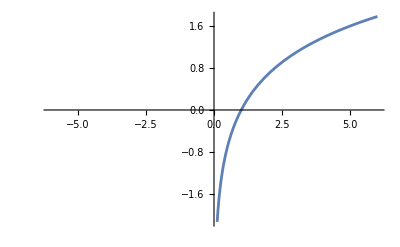

```mathematica
Plot[Log[e],{e,-6,6}]
```